## Omega as function of the coupling angle θ

## [0,180] interval

```mathematica
omega={1.05842,1.05886,1.0592,1.05944,1.05958,1.05962,1.05956,1.0594,1.05913,1.05877,1.0583,1.05774,1.05707,1.0563,1.05543,1.05447,1.0534,1.05223,1.05097,1.0496,1.04814,1.04658,1.04492,1.04316,1.04131,1.03936,1.03732,1.03518,1.03295,1.03062,1.0282,1.02569,1.02308,1.02039,1.01761,1.01473,1.01177,1.00872,1.00558,1.00236,0.999057,0.995667,0.992194,0.988639,0.985004,0.981289,0.977495,0.973624,0.969677,0.965654,0.961557,0.957388,0.953147,0.948836,0.944455,0.940007,0.935493,0.930913,0.926269,0.921563,0.916796,0.91197,0.907085,0.902144,0.897147,0.892096,0.886993,0.88184,0.876637,0.871386,0.866089,0.860747,0.855362,0.849936,0.84447,0.838966,0.833425,0.82785,0.822241,0.8166,0.810929,0.805231,0.799505,0.793755,0.787982,0.782187,0.776372,0.77054,0.764691,0.758828,0.752953,0.747066,0.74117,0.735267,0.729358,0.723445,0.71753,0.711615,0.705702,0.699791,0.693886,0.687988,0.682098,0.676219,0.670352,0.664499,0.658662,0.652843,0.647043,0.641264,0.635508,0.629777,0.624073,0.618397,0.61275,0.607136,0.601555,0.59601,0.590501,0.585032,0.579603,0.574216,0.568873,0.563576,0.558327,0.553126,0.547976,0.542879,0.537836,0.532848,0.527918,0.523047,0.518236,0.513488,0.508804,0.504185,0.499633,0.495149,0.490736,0.486394,0.482125,0.477931,0.473813,0.469772,0.46581,0.461928,0.458128,0.45441,0.450778,0.44723,0.44377,0.440398,0.437115,0.433923,0.430822,0.427814,0.4249,0.422082,0.419359,0.416734,0.414206,0.411777,0.409449,0.407221,0.405094,0.40307,0.401149,0.399331,0.397617,0.396009,0.394506,0.393109,0.391818,0.390634,0.389557,0.388587,0.387725,0.386971,0.386325,0.385787,0.385357};
omegaPrime={0.385357,0.385787,0.386325,0.386971,0.387725,0.388587,0.389557,0.390634,0.391818,0.393109,0.394506,0.396009,0.397617,0.399331,0.401149,0.40307,0.405094,0.407221,0.409449,0.411777,0.414206,0.416734,0.419359,0.422082,0.4249,0.427814,0.430822,0.433923,0.437115,0.440398,0.44377,0.44723,0.450778,0.45441,0.458128,0.461928,0.46581,0.469772,0.473813,0.477931,0.482125,0.486394,0.490736,0.495149,0.499633,0.504185,0.508804,0.513488,0.518236,0.523047,0.527918,0.532848,0.537836,0.542879,0.547976,0.553126,0.558327,0.563576,0.568873,0.574216,0.579603,0.585032,0.590501,0.59601,0.601555,0.607136,0.61275,0.618397,0.624073,0.629777,0.635508,0.641264,0.647043,0.652843,0.658662,0.664499,0.670352,0.676219,0.682098,0.687988,0.693886,0.699791,0.705702,0.711615,0.71753,0.723445,0.729358,0.735267,0.74117,0.747066,0.752953,0.758828,0.764691,0.77054,0.776372,0.782187,0.787982,0.793755,0.799505,0.805231,0.810929,0.8166,0.822241,0.82785,0.833425,0.838966,0.84447,0.849936,0.855362,0.860747,0.866089,0.871386,0.876637,0.88184,0.886993,0.892096,0.897147,0.902144,0.907085,0.91197,0.916796,0.921563,0.926269,0.930913,0.935493,0.940007,0.944455,0.948836,0.953147,0.957388,0.961557,0.965654,0.969677,0.973624,0.977495,0.981289,0.985004,0.988639,0.992194,0.995667,0.999057,1.00236,1.00558,1.00872,1.01177,1.01473,1.01761,1.02039,1.02308,1.02569,1.0282,1.03062,1.03295,1.03518,1.03732,1.03936,1.04131,1.04316,1.04492,1.04658,1.04814,1.0496,1.05097,1.05223,1.0534,1.05447,1.05543,1.0563,1.05707,1.05774,1.0583,1.05877,1.05913,1.0594,1.05956,1.05962,1.05958,1.05944,1.0592,1.05886,1.05842};
```

### Graphical representation of the two sets

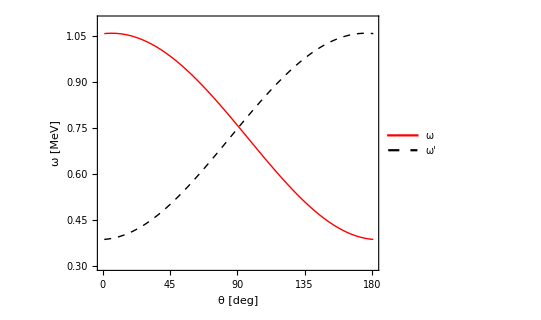

```mathematica
ListPlot[{omega,omegaPrime},Joined->True,PlotRange->{0.3,1.1},AspectRatio->0.8,Frame->True,Axes->False,FrameLabel->{"θ [deg]","ω [MeV]"},PlotLegends->Placed[{"ω","ω'"},{0.20,0.70}],FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Black,Dashed,Thick}},FrameTicks->{{Automatic,None},{{0,45,90,135,180},None}},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"}]
```

## [-180,0] interval

```mathematica
omega={0.385357,0.385035,0.384822,0.384716,0.384719,0.384829,0.385046,0.385371,0.385803,0.386342,0.386986,0.387736,0.388592,0.389552,0.390617,0.391785,0.393056,0.394429,0.395904,0.39748,0.399156,0.400931,0.402805,0.404777,0.406846,0.409011,0.411271,0.413625,0.416072,0.418612,0.421243,0.423964,0.426775,0.429674,0.43266,0.435732,0.43889,0.442131,0.445455,0.448861,0.452347,0.455913,0.459557,0.463279,0.467076,0.470948,0.474893,0.47891,0.482998,0.487156,0.491383,0.495676,0.500036,0.50446,0.508947,0.513496,0.518105,0.522774,0.5275,0.532283,0.53712,0.542011,0.546955,0.551949,0.556992,0.562083,0.56722,0.572402,0.577628,0.582895,0.588203,0.593549,0.598933,0.604352,0.609806,0.615292,0.620809,0.626356,0.63193,0.63753,0.643156,0.648804,0.654473,0.660163,0.66587,0.671594,0.677332,0.683084,0.688847,0.69462,0.700402,0.706189,0.711982,0.717777,0.723574,0.729371,0.735166,0.740957,0.746743,0.752521,0.758292,0.764051,0.769799,0.775533,0.781251,0.786953,0.792635,0.798297,0.803937,0.809553,0.815144,0.820708,0.826243,0.831747,0.83722,0.842659,0.848063,0.85343,0.858758,0.864047,0.869294,0.874498,0.879657,0.88477,0.889835,0.894851,0.899816,0.904729,0.909589,0.914393,0.919141,0.92383,0.928461,0.93303,0.937537,0.941981,0.94636,0.950673,0.954918,0.959094,0.963201,0.967236,0.971199,0.975088,0.978902,0.98264,0.986301,0.989884,0.993387,0.996811,1.00015,1.00341,1.00659,1.00968,1.01268,1.0156,1.01844,1.02118,1.02384,1.0264,1.02888,1.03126,1.03356,1.03575,1.03786,1.03987,1.04179,1.04361,1.04534,1.04697,1.0485,1.04994,1.05128,1.05252,1.05366,1.0547,1.05564,1.05649,1.05723,1.05788,1.05842};
omegaPrime={1.05842,1.05788,1.05723,1.05649,1.05564,1.0547,1.05366,1.05252,1.05128,1.04994,1.0485,1.04697,1.04534,1.04361,1.04179,1.03987,1.03786,1.03575,1.03356,1.03126,1.02888,1.0264,1.02384,1.02118,1.01844,1.0156,1.01268,1.00968,1.00659,1.00341,1.00015,0.996811,0.993387,0.989884,0.986301,0.98264,0.978902,0.975088,0.971199,0.967236,0.963201,0.959094,0.954918,0.950673,0.94636,0.941981,0.937537,0.93303,0.928461,0.92383,0.919141,0.914393,0.909589,0.904729,0.899816,0.894851,0.889835,0.88477,0.879657,0.874498,0.869294,0.864047,0.858758,0.85343,0.848063,0.842659,0.83722,0.831747,0.826243,0.820708,0.815144,0.809553,0.803937,0.798297,0.792635,0.786953,0.781251,0.775533,0.769799,0.764051,0.758292,0.752521,0.746743,0.740957,0.735166,0.729371,0.723574,0.717777,0.711982,0.706189,0.700402,0.69462,0.688847,0.683084,0.677332,0.671594,0.66587,0.660163,0.654473,0.648804,0.643156,0.63753,0.63193,0.626356,0.620809,0.615292,0.609806,0.604352,0.598933,0.593549,0.588203,0.582895,0.577628,0.572402,0.56722,0.562083,0.556992,0.551949,0.546955,0.542011,0.53712,0.532283,0.5275,0.522774,0.518105,0.513496,0.508947,0.50446,0.500036,0.495676,0.491383,0.487156,0.482998,0.47891,0.474893,0.470948,0.467076,0.463279,0.459557,0.455913,0.452347,0.448861,0.445455,0.442131,0.43889,0.435732,0.43266,0.429674,0.426775,0.423964,0.421243,0.418612,0.416072,0.413625,0.411271,0.409011,0.406846,0.404777,0.402805,0.400931,0.399156,0.39748,0.395904,0.394429,0.393056,0.391785,0.390617,0.389552,0.388592,0.387736,0.386986,0.386342,0.385803,0.385371,0.385046,0.384829,0.384719,0.384716,0.384822,0.385035,0.385357};
omegaTable=Table[{-180+(i-1),omega[[i]]},{i,1,Length[omega]}];
omegaPrimeTable=Table[{-180+(i-1),omegaPrime[[i]]},{i,1,Length[omegaPrime]}];
```

### Graphical representation of the two sets

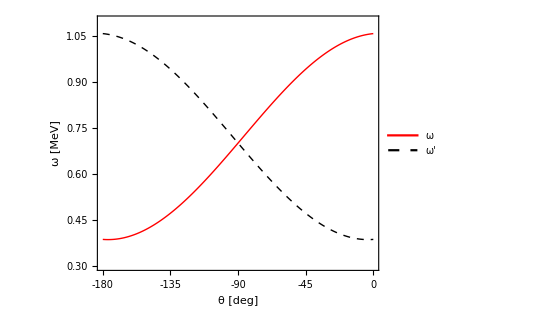

```mathematica
ListPlot[{omegaTable,omegaPrimeTable},Joined->True,PlotRange->{0.3,1.1},AspectRatio->0.8,Frame->True,Axes->False,FrameLabel->{"θ [deg]","ω [MeV]"},PlotLegends->Placed[{"ω","ω'"},{0.20,0.60}],FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Black,Dashed,Thick}},FrameTicks->{{Automatic,None},{{-180,-135,-90,-45,0},None}},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"}]
```